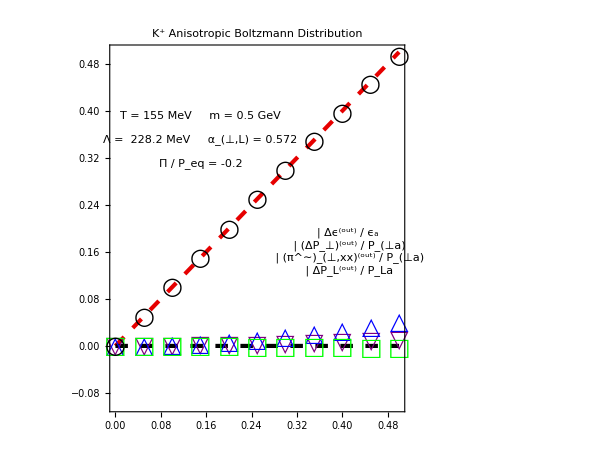

```mathematica
(*MASSIVE ANISOTROPIC BOLTZMANN GAS*)

T0 = 0.155;
mass = 0.5;  (* kaon mass scale *)
sign = 0;
αT = 0.572049;
αL = 0.572049;
Λ = 0.22824; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,9.52952*10^-05,0.000381185,0.000857675,0.00152477,0.00238249,0.00343085,0.00466985,0.00609951,0.00771985,0.00953086};

ΔPToverPTdata = {0.0,0.00039967,0.00159882,0.00359794,0.00639781,0.00999953,0.0144045,0.0196145,0.0256314,0.0324576,0.0400955};

ΔPLoverPLdata = {0.0,-4.15993*10^-05,-0.000166453,-0.000374725,-0.000666693,-0.00104274,-0.00150336,-0.00204915,-0.00268081,-0.00339914,-0.00420505};

piperpoverPTdata = {0.0,0.049994,0.0999521,0.149838,0.199617,0.249251,0.298706,0.347946,0.396935,0.445637,0.494016};

style={Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out) / ϵ_a",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["(ΔP_⊥)^(out) / P_(⊥a)",FontSize->14]},
{Graphics[{Directive[Thick,Black],Circle[]},ImageSize->16],Style["(π^∼)_(⊥,xx)^(out) / P_(⊥a)",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->16],Style["ΔP_L^(out) / P_La",FontSize->14]}}],Background->White];

legend2=Panel[Grid[{{Style["T = 155 MeV     m = 0.5 GeV",FontSize->14]},{},
{Style["Λ =  228.2 MeV     α_(⊥,L) = 0.572",FontSize->14]},{},{Style["Π / P_eq = -0.2",FontSize->14]}}],Background->White];


Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΔPToverPTplot,ΔPLoverPLplot,piperpoverPTplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{□,24},{○,24}},PlotStyle->{Purple,Blue,Green,Black},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->{Inset[legend1,{0.41,0.16}],Inset[legend2,{0.15,0.35}]},ImageSize->{600,500},FrameLabel->{"(π^∼)_(⊥,xx)^(in) / P_(⊥a)"},PlotLabel->Style["K^+ Anisotropic Boltzmann Distribution",FontSize->22]]
```